# Maximal Variety and Leibnizian Paths

Authors: Furkan Semih Dündar, Xerxes D. Arsiwalla, Hatem Elshatlawy
Year: 2025
License: CC BY-SA 4.0

## Software

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<wws25fsd`
```

```mathematica
<<Wolfram`Multicomputation`
```

## The Multiway System

```mathematica
mw=MultiwaySystem[{"BA"->"AB"},"ABAABBABABA",Method->{"String","Cyclic"->True}]["StatesGraph",3,"CanonicalStateFunction"->Full,PlotTheme->"VibrantColor"]
```

-Graphics-

```mathematica
HighlightGraph[mw,PhysicalMultiwaySystem[mw,VarRule[mw]]]
```

-Graphics-

## Last strings

```mathematica
bg=MultiwaySystem[{"BA"->"AB"},"ABAABBABABA",Method->{"String","Cyclic"->True}]["BranchialGraph",3,"CanonicalStateFunction"->Full]
```

-Graphics-

```mathematica
lv=VertexList[bg]
```

{AAAABBABBAB,AAAABBBAABB,BBBABAABAAA,AAABAABBBAB,AAABABABABB,AABAABABABB,AABABAABABB,AAABABABBAB,AAABBABBAAB,BBBAABABAAA,BBBAABAABAA,AABABABABAB,AAABBAABABB,AAABBABAABB,AABAABBAABB}

```mathematica
Length[lv]
```

15

```mathematica
lvleib=Select[lv,Variety[#]>0&]
```

{AAAABBABBAB,AAAABBBAABB,BBBABAABAAA,AAABAABBBAB,AAABABABABB,AABAABABABB,AABABAABABB,AAABABABBAB,AAABBABBAAB,BBBAABABAAA,AAABBAABABB,AAABBABAABB}

```mathematica
Length[lvleib]
```

12

```mathematica
var=VarRule[mw]
```

{AABAABBABAB→5,AAABABBABAB→13/3,AABAABABBAB→0,AABAABBAABB→0,AABABAABBAB→25/6,AAAABBBABAB→17/3,AAABABABBAB→13/3,AAABABBAABB→6,BBBABAABAAA→20/3,AABAABABABB→5,AABABAABABB→25/6,AABABABAABB→0,AAABBAABBAB→6,AAAABBABBAB→31/6,AAAABBBAABB→25/6,AAABAABBBAB→20/3,AAABABABABB→16/3,AAABBABBAAB→37/6,BBBAABABAAA→19/3,BBBAABAABAA→0,AABABABABAB→0,AAABBAABABB→6,AAABBABAABB→6}

## Calculations

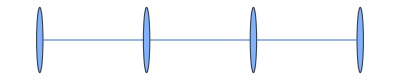
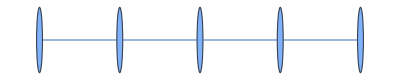
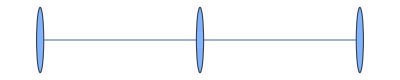
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
paths=Flatten[PathsBetween[mw,"AABAABBABAB",#,4]&/@lvleib,1]
```

```mathematica
HighlightGraph[mw,PhysicalMultiwaySystem[mw,var]]
```

-Graphics-

```mathematica
ma=Select[ActionOnPath[#,var]&/@paths,NumberQ]//Max
```

85/3

```mathematica
maPaths=Select[paths,ActionOnPath[#,var]==ma&]
```

{-Graphics-}

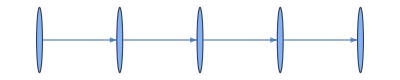

```mathematica
maPathsDir=DirectedGraph[#,"Acyclic"]&/@maPaths
```

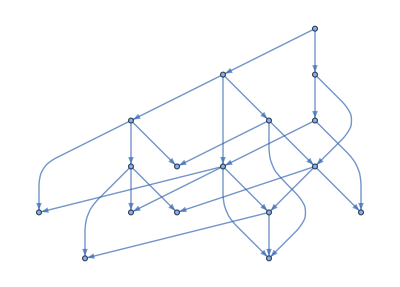

```mathematica
physPaths=GraphUnion@@(DirectedGraph[#,"Acyclic"]&/@Select[paths,ActionOnPath[#,var]>0&])
```

```mathematica
mwPlt=HighlightGraph[Graph[mw,GraphHighlightStyle->"Solid"],{Style[physPaths,Darker[Red],Thick],Style[maPathsDir,Darker[Green],Thick]},ImageSize->900]
```

-Graphics-